```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test.txt","Table"];
cx=data⟦1;;(Length@data+1)/3⟧;
cy=data⟦(Length@data+1)/3+1;;(Length@data+1)/3*2⟧;
h=data⟦(Length@data+1)2/3+1;;-1⟧;
Length@data
```

3002

```mathematica
"
```

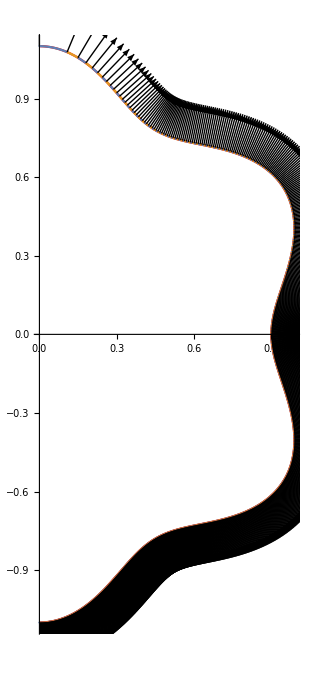

```mathematica
Subscript[sx, i_][t_]:=cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5)
Subscript[sy, i_][t_]:=cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5)
p[θ_]=(1+0.1Cos[6θ]){Sin[θ],Cos[θ]};
ar=Table[Arrow[{{Subscript[sx, i][0],Subscript[sy, i][0]},{Subscript[sx, i][0],Subscript[sy, i][0]}+0.15Normalize@{-Subscript[sy, i]'[0],Subscript[sx, i]'[0]}}],{i,1,Length@cx-1}];
Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,Length@cx-1}];
Show[ListPlot[Transpose[{cx⟦All,1⟧,cy⟦All,1⟧}]],ParametricPlot[p[θ],{θ,0,π},PlotStyle->Red],
ParametricPlot[{%⟦1;;-1;;2⟧,%⟦2;;-1;;2⟧},{t,0,1}],
Graphics[{ar}],AspectRatio->Automatic,ImageSize->Medium]
Table[{t+i,Subscript[sy, i]''[t]/h⟦i⟧^2},{i,1,Length@cx-1}];
Show[
ParametricPlot[{%⟦1;;-1;;2⟧,%⟦2;;-1;;2⟧},{t,0,1},AspectRatio->Automatic,PlotRange->All]
,AspectRatio->0.5]
```

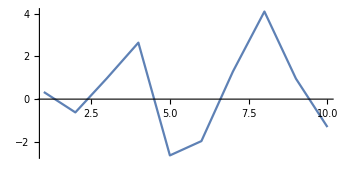

```mathematica
Clear[i,kv]
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5
ParallelTable[{0+i,Subscript[kv, i][0]+1},{i,1,Length@cx-1}];
Show[
ListPlot[%,PlotRange->All,Joined->True],AspectRatio->0.5]
```

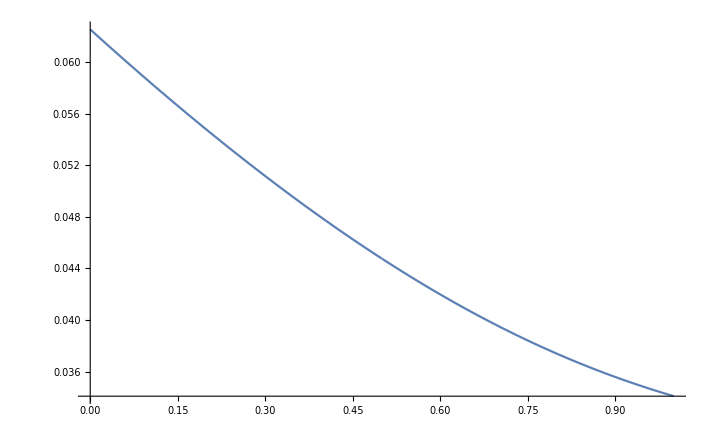

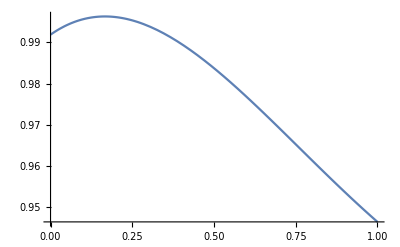

```mathematica
i=2;
j=2;
r=Subscript[sx, i][t];
z=Subscript[sy, i][t];
(*{rp,zp}={cx⟦j,1⟧,cy⟦j,1⟧};*)
{rp,zp}={r,z}/.t->0.5;
a=rp^2+r^2+(zp-z)^2;
b=2 rp r;
m=2 b/(a+b);
Plot[Evaluate@D[((1-m)/(Abs@((t-0.5)^2))),{t,0}],{t,0,1},PlotRange->Full,PlotPoints->100]
```

```mathematica
{r,z}/.t->1
{rp,zp}
```

{0.917393,0.917393}

{0.615279,0.726817}